```mathematica
(*2.4a*)
(*Using a numerical method of your choice,find the value μ=Subscript[μ, c] where the system undergoes a homoclinic bifurcation. Give your result with two significant digits.*)
f1[x_,y_]:=μ*x+y-x^2;
f2[x_,y_]:=-x+μ*y+2x^2;
(*Calc. the fixed points*)
fixedP=Solve[{f1[x,y]==0,f2[x,y]==0},{x,y}];
(*Calc. the eigenvalues of the second fixed point*)
jacobian=Grad[{f1[x,y],f2[x,y]},{x,y}];
jacobian2=jacobian/. fixedP[[2]];
eigVal=Eigenvalues[jacobian2];
unstableVal=eigVal[[2]];
M=Eigenvectors[jacobian2];
unstableM = M[[2]];
(*Trajectory from saddle in unstable direction*)
tstep=0.001;
sol[μTmp_,T_]:=NDSolve[Join[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2x[t]^2},Thread[{x[0],y[0]}=={fixedP[[2]][[1]][[2]],fixedP[[2]][[2]][[2]]}-tstep*unstableM]]/. μ->μTmp,{x[t],y[t]},{t,0,T}];
(*We can use to vary the value on μ and see where it breaks*)
Manipulate[ParametricPlot[Evaluate[{x[t],y[t]}/. sol[μTmp,20]],{t,0,20}],{μTmp,-0.1,0.1,tstep}]
(*We can see that μc=0.066-which is in agreement with the book*)
```

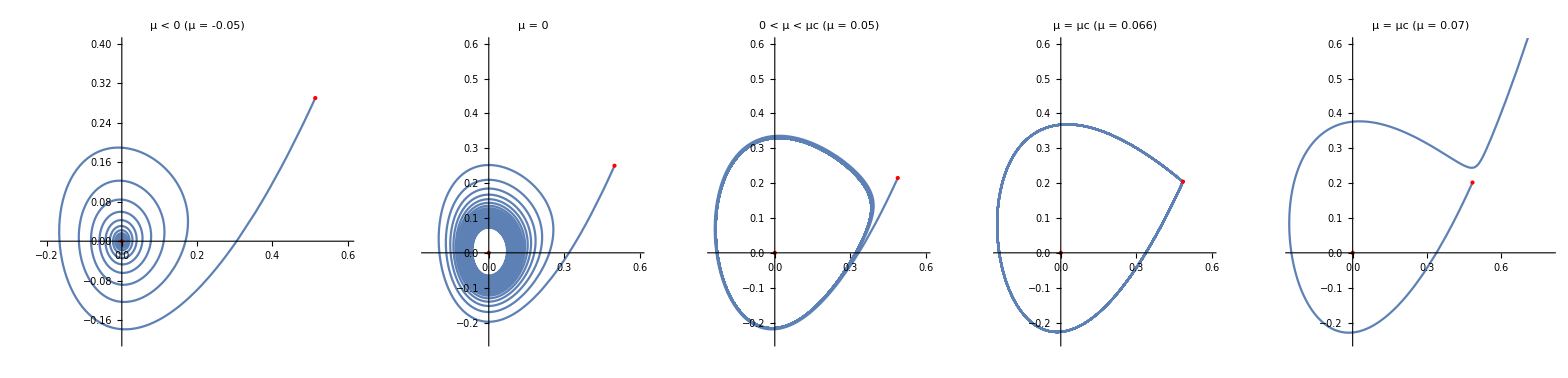

```mathematica
(*2.4b*)
(*Plot the phase portraits that occur for the cases μ<0, μ=0, 0<μ<Subscript[μ, c] and μ=Subscript[μ, c]​​*)
μc = 0.066;
fp1=Graphics[{Red,Point[{0,0}]}];fp21=Graphics[{Red,Point[{fixedP[[2]][[1]][[2]],fixedP[[2]][[2]][[2]]}/. μ->-0.05]}];fp22=Graphics[{Red,Point[{fixedP[[2]][[1]][[2]],fixedP[[2]][[2]][[2]]}/. μ->0]}];fp23=Graphics[{Red,Point[{fixedP[[2]][[1]][[2]],fixedP[[2]][[2]][[2]]}/. μ->0.05]}];fp24=Graphics[{Red,Point[{fixedP[[2]][[1]][[2]],fixedP[[2]][[2]][[2]]}/. μ->μc]}];fp25=Graphics[{Red,Point[{fixedP[[2]][[1]][[2]],fixedP[[2]][[2]][[2]]}/. μ->0.07]}];

p1=ParametricPlot[Evaluate[{x[t],y[t]}/. sol[-0.05,200]],{t,0,200},PlotRange->{{-0.2,0.6},{-0.2,0.4}},PlotLabel->"μ < 0\n(μ = -0.05)"];
p2=ParametricPlot[Evaluate[{x[t],y[t]}/. sol[0,200]],{t,0,200},PlotRange->{{-0.25,0.6},{-0.25,0.6}},PlotLabel->"μ = 0"];
p3=ParametricPlot[Evaluate[{x[t],y[t]}/. sol[0.05,200]],{t,0,200},PlotRange->{{-0.25,0.6},{-0.25,0.6}},PlotLabel->"0 < μ < μc\n(μ = 0.05)"];
p4=ParametricPlot[Evaluate[{x[t],y[t]}/. sol[μc,200]],{t,0,200},PlotRange->{{-0.25,0.6},{-0.25,0.6}},PlotLabel->"μ = μc\n(μ = 0.066)"];
p5=ParametricPlot[Evaluate[{x[t],y[t]}/. sol[0.07,20]],{t,0,20},PlotRange->{{-0.25,0.8},{-0.25,0.6}},PlotLabel->"μ = μc\n(μ = 0.07)"];
GraphicsRow[{Show[p1,fp1,fp21],Show[p2,fp1,fp22],Show[p3,fp1,fp23],Show[p4,fp1,fp24],Show[p5,fp1,fp25]},ImageSize->Full]
```

```mathematica
(*2.4c*)
(*Find an analytical expression for the time (t​)_1 to escape from the saddle to x((t​)_1)=1*)
solution = DSolve[{x'[t] == u* x[t], y'[t] == s*y[t], x[0] ==γ , y [0] == 1},{x[t],y[t]},t];
Solve[(x[t]/. Part[solution,1,1])==1,t]
```

```mathematica
{{t->ConditionalExpression[(2 ⅈ π C[1]+Log[1/γ])/u, C[1]∈Integers]}}
(*t = log(1/γ)/u*)
```

```mathematica
(*2.4d*)
(*Find an analytical expression for u suitable for the system in Eq.(1)*)
(*We can obtain u from the eigenvalue *)
eig2 = eigVal[[2]]
```

(-1+2 μ+√(5+9 μ^2+4 μ^3+μ^4))/(2+μ)

```mathematica
(*2.4e*)
(*Give your estimate for aa with one digit accuracy.*)
(*With the help of c,d and e we can rewrite the function:*)
ab=Normal[NonlinearModelFit[Table[Abs[μ-0.066], {μ, 0, 0.066}],Log[A*x^a], {a, A}, x]]
ab2 = ab/.x->1
(*A=0.7 and a=1*)
```

Log[1.06823 x^1.]

0.066

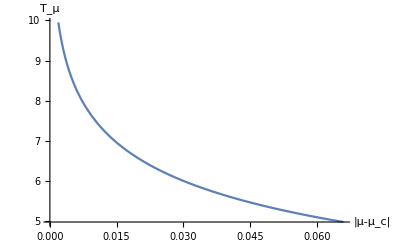

```mathematica
(*2.4f*)
(*Numerically evaluate the period time of the periodic orbit and plot it against μ−Subscript[μ, c]*)
μc = 0.066;
(* 2.4f *)
func[x_, a_, A_] = -Log[A*x^a]/eig2 /.μ-> {Subscript[μ, c]-x};
Plot[{func[x, a, A] /. {a-> 1, A -> 0.7}}, {x, 0,Subscript[μ, c]}, AxesLabel->{"|μ-μ_c|","T_μ"}]
```